```mathematica
ClearAll["Global`*"]
```

This notebook accompanies the paper, “Quasinormal modes analysis of a massive scalar field in a Schwarzschild background via the Spectral Method”, by Davide Batic, Anna Chrysostomou, Alan S. Cornell, and Denys Dutykh.
Figures 1 and 2 were generated with this notebook.

A. Chrysostomou

### Massive scalar QNM within the Schwarzschild background

```mathematica
This notebook contains the effective potential for the massive scalar QNM, 
plotted with respect to the radial coordinate r and the parametrisation x=r/2M.
We also sketch the parameter space for two benchmark points,
μ = 0.5, L = 2 and μ = 0.5, L = 6, where L = l(l+1).
```

```mathematica
V[r_,l_,M_,μ_]:= ( 1-(2 M)/r)*((l(l+1))/r^2+(2 M)/r^3+μ^2);
```

```mathematica
Vtilde[x_,l_,mu_]:=(1-1/x)*((l (l+1))/(4*x^2)+1/(4*x^3)+mu^2);
```

```mathematica
VL[r_,L_,mu_]:=( 1-2/r)*(L/r^2+2/r^3+mu^2);
```

```mathematica
VtiLde[x_,L_,mu_]:=(1-1/x)*(L/(4*x^2)+1/(4*x^3)+mu^2);
```

```mathematica
plotx=Plot[{Vtilde[x,2,3],Vtilde[x,2,1.4],Vtilde[x,2,0.7],Vtilde[x,2,0.1],Vtilde[x,2,0]},{x,0,10},PlotTheme->"Scientific",GridLines->None,PlotRange->{{-0.2,7},{0,1.75}},FrameStyle->Directive[Black],FrameLabel->{Style[ToExpression["x",TeXForm,HoldForm],Black,FontFamily->"TeX Gyre Pagella",FontSize->20],Style[ToExpression["\\widetilde{V}(x)",TeXForm,HoldForm],Black,FontFamily->"TeX Gyre Pagella",FontSize->20]},FrameTicksStyle->Directive[FontSize->Scaled[0.02],Black,FontFamily->"TeX Gyre Pagella"],PlotLegends->Placed[{Style[ToExpression["\\mu = 3",TeXForm,HoldForm],Black,FontSize->Scaled[0.03],FontFamily->"TeX Gyre Pagella"],Style[ToExpression["\\mu = 1.4",TeXForm,HoldForm],Black,FontSize->Scaled[0.03],FontFamily->"TeX Gyre Pagella"],Style[ToExpression["\\mu = 0.7",TeXForm,HoldForm],Black,FontSize->Scaled[0.03],FontFamily->"TeX Gyre Pagella"],Style[ToExpression["\\mu = 0.1",TeXForm,HoldForm],Black,FontSize->Scaled[0.03],FontFamily->"TeX Gyre Pagella"],Style[ToExpression["\\mu = 0 ",TeXForm,HoldForm],Black,FontSize->Scaled[0.03],FontFamily->"TeX Gyre Pagella"]},{{0.1,0.78}}],ImageSize->Large];
```

```mathematica
zoomPlotx=Framed[Plot[{Vtilde[x,2,3],Vtilde[x,2,1.4],Vtilde[x,2,0.7],Vtilde[x,2,0.1],Vtilde[x,2,0]},{x,0,50},PlotRange->{{0.75,17},{0,8.8}},FrameStyle->Directive[Black],FrameLabel->{Style[ToExpression["x",TeXForm,HoldForm],Black,FontFamily->"TeX Gyre Pagella",FontSize->Scaled[0.07]],Style[ToExpression["\\widetilde{V}(x)",TeXForm,HoldForm],Black,FontFamily->"TeX Gyre Pagella",FontSize->Scaled[0.085]]},FrameTicksStyle->Directive[FontSize->Scaled[0.015],FontFamily->"TeX Gyre Pagella"],PlotTheme->"Scientific",ImageSize->250,ImagePadding->{{35,9},{35,0}}],Background->White,(*makes the inset opaque*)FrameStyle->Darker[Gray,0.5]];

(*Combine main plot with inset*)
potentialplotx=Show[plotx,Epilog->{Inset[zoomPlotx,Scaled[{0.73,0.7}]]}]
```

-Graphics-

```mathematica
(*************** FIGURE 2 *****************)
```

```mathematica
plotEq11=Collect[Discriminant[(4*x^3*mu^2-2*L*x^2+3*(L-1)*x+4),x]/4,mu,Simplify];
```

```mathematica
RegionPlot[plotEq11>0,{mu,0.1,2},{L,1,12}];
```

```mathematica
(*Find peak location numerically for the potential w.r.t. x=r/2M*)xPeak[L_?NumericQ,mu_?NumericQ]:=x/. FindMaximum[VtiLde[x,L,mu],{x,2},WorkingPrecision->100][[2]];
```

```mathematica
(*  V_peak>mu^2 -> but we are left with numerical artefacts*)
RegionPlot[VtiLde[xPeak[L,mu],L,mu]>mu^2,{mu,0.1,2},{L,1,12}];
```

```mathematica
(*Find peak location numerically for the potential w.r.t.r*)
rPeak[L_,mu_]:=r/. FindMaximum[VL[r,L,mu],{r,3}][[2]];
```

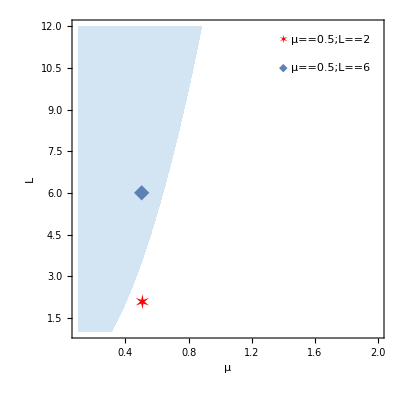

```mathematica
(* V_peak>mu^2 -> this is Fig. 2*)
space=RegionPlot[VL[rPeak[L,mu],L,mu]>mu^2,{mu,0.1,2},{L,1,12},PlotPoints->20,PlotTheme->"Scientific",GridLines->None,FrameStyle->Directive[Black],BoundaryStyle->None,PlotStyle->Darker[LightBlue,0.05],FrameLabel->{Style[ToExpression["\\mu",TeXForm,HoldForm],Black,FontFamily->"TeX Gyre Pagella",FontSize->20],Style[ToExpression["L",TeXForm,HoldForm],Black,FontFamily->"TeX Gyre Pagella",FontSize->20]},Epilog->{Text[Style["◆",ColorData[97][1],20,FontFamily->"TeX Gyre Pagella"],{0.5,6},{0,0}],Text[Style["✶",Red,FontSize->20,FontFamily->"TeX Gyre Pagella"],{0.5,2},{0,0}],Text[Style["◆",ColorData[97][1],FontSize->Scaled[0.04],FontFamily->"TeX Gyre Pagella"],{1.4,10.5},{0,0}],Text[Style["✶",Red,FontSize->Scaled[0.04],FontFamily->"TeX Gyre Pagella"],{1.4,11.5},{0,0}],Text[Style[ToExpression["\\mu = 0.5; \; L= 2",TeXForm,HoldForm],Black,FontSize->Scaled[0.04],FontFamily->"TeX Gyre Pagella"],{1.7,11.5},{0,0}],Text[Style[ToExpression["\\mu = 0.5; \; L = 6",TeXForm,HoldForm],Black,FontSize->Scaled[0.04],FontFamily->"TeX Gyre Pagella"],{1.7,10.5},{0,0}]},FrameTicksStyle->Directive[FontSize->Scaled[0.02],Black,FontFamily->"TeX Gyre Pagella"]]
```

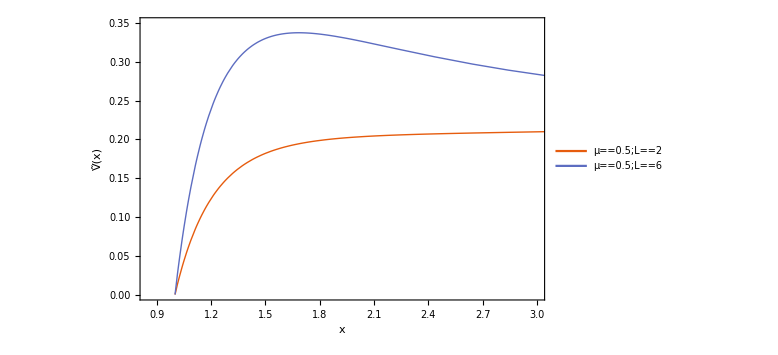

```mathematica
space2=Plot[{Vtilde[x,1,0.5],Vtilde[x,2,0.5]},{x,0,10},PlotTheme->"Scientific",GridLines->None,PlotRange->{{0.85,3},{0,0.35}},FrameStyle->Directive[Black],PlotStyle->Thick,FrameLabel->{Style[ToExpression["x",TeXForm,HoldForm],Black,FontFamily->"TeX Gyre Pagella",FontSize->25],Style[ToExpression["\\widetilde{V}(x)",TeXForm,HoldForm],Black,FontFamily->"TeX Gyre Pagella",FontSize->25]},PlotLegends->Placed[{Style[ToExpression["\\mu = 0.5; L= 2",TeXForm,HoldForm],Black,FontSize->Scaled[0.04],FontFamily->"TeX Gyre Pagella"],Style[ToExpression["\\mu = 0.5; L = 6",TeXForm,HoldForm],Black,FontSize->Scaled[0.04],FontFamily->"TeX Gyre Pagella"]},{{0.825,0.15}}],FrameTicksStyle->Directive[FontSize->Scaled[0.03],Black,FontFamily->"TeX Gyre Pagella"],ImageSize->Large]
```